## Plots

```mathematica
SetDirectory["/Users/shainen/Dropbox/Research/bhsucon/nb/nb/"];
```

```mathematica
Get["constants.m"]
```

```mathematica
QM=ListPlot[{times,AvgJzS/10}ᵀ,Joined->True];
```

```mathematica
QMw=ListPlot[{times,(AvgJz2-AvgJzS^2/10)/10}ᵀ,Joined->True];
```

```mathematica
Get["data/su3awS10t10j0.01r100000spn.lst"];
```

```mathematica
Get["data/su3awS10t10j0.01r100000corn.lst"];
```

```mathematica
TWAsu3=ListPlot[Table[{times[[1;;TE]],2avgspins3[[1;;TE,n]]}ᵀ,{n,1,2}],Joined->True,PlotStyle->Dashed];
```

```mathematica
TWAsu3w=ListPlot[Table[{times[[1;;TE]],4avgcor3[[1;;TE,n]]}ᵀ-4avgspins3[[1;;TE,n-2]],{n,3,4}],Joined->True,PlotStyle->Dotted];
```

```mathematica
TWAsu3w8=ListPlot[Table[{times[[1;;TE]],2/3(1-√3 avgcor3[[1;;TE,n]])-4 avgspins3[[1;;TE,n]]^2}ᵀ,{n,1,2}],Joined->True,PlotStyle->Dashed];
```

```mathematica
Get["data/su2awS3t200j0.01r100000sp.lst"];
```

```mathematica
Get["data/su2awS3t200j0.01r100000cor.lst"];
```

```mathematica
TWAsu2=ListPlot[Table[{times[[1;;TE]],avgspins2[[1;;TE,n,3]]}ᵀ,{n,1,3}],Joined->True,PlotStyle->Dotted];
```

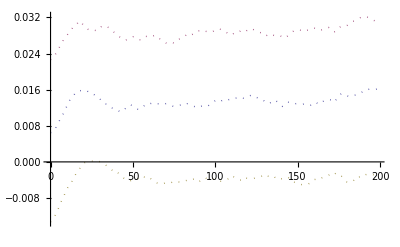

```mathematica
TWAsu2w=ListPlot[Table[{times[[1;;TE]],avgcor2[[1;;TE,n,n,3]]-1/8-avgspins2[[1;;TE,n,3]]^2}ᵀ,{n,1,3}],Joined->True,PlotStyle->Dotted]
```

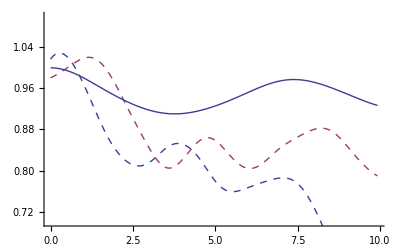

```mathematica
Show[TWAsu3,QM,PlotRange->{0.7,1.1},AxesOrigin->{0,-1.1}]
```

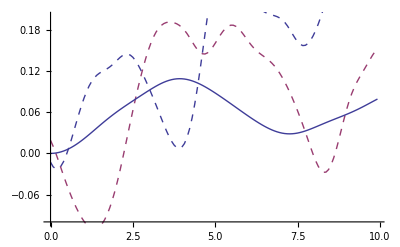

```mathematica
Show[TWAsu3w8,QMw,PlotRange->{-0.1,0.2},AxesOrigin->{0,-0.1}]
```

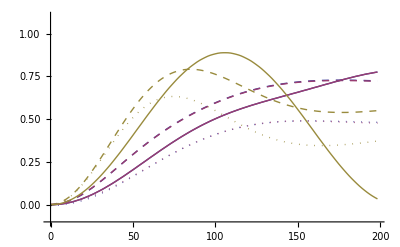

```mathematica
Show[TWAsu3w8,TWAsu3w,QMw,PlotRange->{-0.1,1.1},AxesOrigin->{0,-0.1}]
```